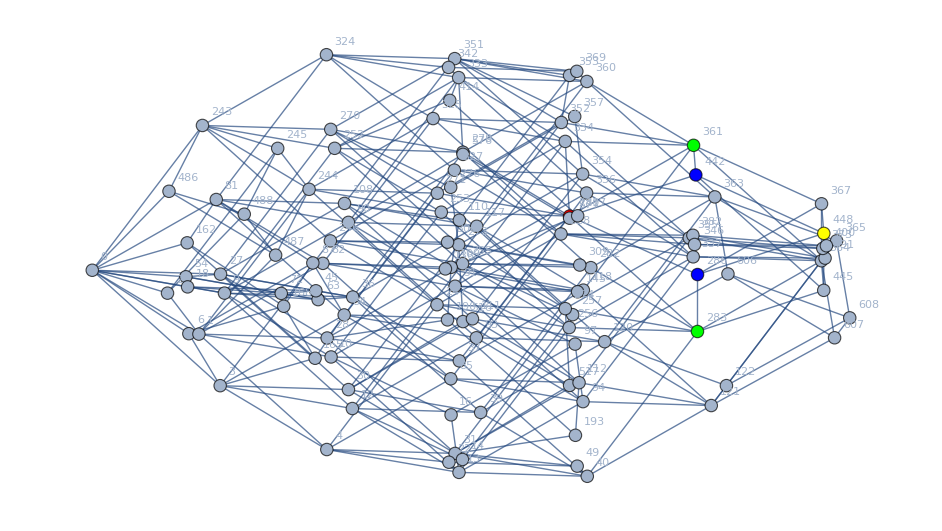

```mathematica
Monitor[
Graph[DeleteDuplicates[Flatten[
Table[
With[
{current=newAssoc[key]},
Table[
Sort[current["signature"]<->l],
{l,current["links"]}
]
]
,{key,Sort[Keys[newAssoc]]}
]
]],
GraphLayout->"HighDimensionalEmbedding", VertexLabels->"Name", 
VertexStyle->{280->Red,283->Green,361->Green,442->Blue,286->Blue,448->Yellow}],key
]
```

```mathematica
Sort[5<->3]
```

3<->5

```mathematica
Graph[{0<->243,0<->486,0<->81,0<->162,0<->27,0<->54,0<->9,0<->18,0<->3,0<->6,0<->1,0<->2,243<->486,243<->0,243<->324,243<->405,243<->270,243<->297,243<->252,243<->261,243<->246,243<->249,243<->244,243<->245,81<->324,81<->567,81<->162,81<->0,81<->108,81<->135,81<->90,81<->99,81<->84,81<->87,81<->82,81<->83,27<->270,27<->513,27<->108,27<->189,27<->54,27<->0,27<->36,27<->45,27<->30,27<->33,27<->28,27<->29,9<->252,9<->495,9<->90,9<->171,9<->36,9<->63,9<->18,9<->0,9<->12,9<->15,9<->10,9<->11,3<->246,3<->489,3<->84,3<->165,3<->30,3<->57,3<->12,3<->21,3<->6,3<->0,3<->4,3<->5,1<->244,1<->487,1<->82,1<->163,1<->28,1<->55,1<->10,1<->19,1<->4,1<->7,1<->2,1<->0,324<->567,324<->81,324<->405,324<->243,324<->351,324<->378,324<->333,324<->342,324<->327,324<->330,324<->325,324<->326,270<->513,270<->27,270<->351,270<->432,270<->297,270<->243,270<->279,270<->288,270<->273,270<->276,270<->271,270<->272,252<->495,252<->9,252<->333,252<->414,252<->279,252<->306,252<->261,252<->243,252<->255,252<->258,252<->253,252<->254,246<->489,246<->3,246<->327,246<->408,246<->273,246<->300,246<->255,246<->264,246<->249,246<->243,246<->247,246<->248,244<->487,244<->1,244<->325,244<->406,244<->271,244<->298,244<->253,244<->262,244<->247,244<->250,244<->245,244<->243,108<->351,108<->594,108<->189,108<->27,108<->135,108<->81,108<->117,108<->126,108<->111,108<->114,108<->109,108<->110,90<->333,90<->576,90<->171,90<->9,90<->117,90<->144,90<->99,90<->81,90<->93,90<->96,90<->91,90<->92,84<->327,84<->570,84<->165,84<->3,84<->111,84<->138,84<->93,84<->102,84<->87,84<->81,84<->85,84<->86,82<->325,82<->568,82<->163,82<->1,82<->109,82<->136,82<->91,82<->100,82<->85,82<->88,82<->83,82<->81,36<->279,36<->522,36<->117,36<->198,36<->63,36<->9,36<->45,36<->27,36<->39,36<->42,36<->37,36<->38,30<->273,30<->516,30<->111,30<->192,30<->57,30<->3,30<->39,30<->48,30<->33,30<->27,30<->31,30<->32,28<->271,28<->514,28<->109,28<->190,28<->55,28<->1,28<->37,28<->46,28<->31,28<->34,28<->29,28<->27,12<->255,12<->498,12<->93,12<->174,12<->39,12<->66,12<->21,12<->3,12<->15,12<->9,12<->13,12<->14,10<->253,10<->496,10<->91,10<->172,10<->37,10<->64,10<->19,10<->1,10<->13,10<->16,10<->11,10<->9,4<->247,4<->490,4<->85,4<->166,4<->31,4<->58,4<->13,4<->22,4<->7,4<->1,4<->5,4<->3,351<->594,351<->108,351<->432,351<->270,351<->378,351<->324,351<->360,351<->369,351<->354,351<->357,351<->352,351<->353,333<->576,333<->90,333<->414,333<->252,333<->360,333<->387,333<->342,333<->324,333<->336,333<->339,333<->334,333<->335,327<->570,327<->84,327<->408,327<->246,327<->354,327<->381,327<->336,327<->345,327<->330,327<->324,327<->328,327<->329,325<->568,325<->82,325<->406,325<->244,325<->352,325<->379,325<->334,325<->343,325<->328,325<->331,325<->326,325<->324,279<->522,279<->36,279<->360,279<->441,279<->306,279<->252,279<->288,279<->270,279<->282,279<->285,279<->280,279<->281,273<->516,273<->30,273<->354,273<->435,273<->300,273<->246,273<->282,273<->291,273<->276,273<->270,273<->274,273<->275,271<->514,271<->28,271<->352,271<->433,271<->298,271<->244,271<->280,271<->289,271<->274,271<->277,271<->272,271<->270,255<->498,255<->12,255<->336,255<->417,255<->282,255<->309,255<->264,255<->246,255<->258,255<->252,255<->256,255<->257,253<->496,253<->10,253<->334,253<->415,253<->280,253<->307,253<->262,253<->244,253<->256,253<->259,253<->254,253<->252,247<->490,247<->4,247<->328,247<->409,247<->274,247<->301,247<->256,247<->265,247<->250,247<->244,247<->248,247<->246,117<->360,117<->603,117<->198,117<->36,117<->144,117<->90,117<->126,117<->108,117<->120,117<->123,117<->118,117<->119,111<->354,111<->597,111<->192,111<->30,111<->138,111<->84,111<->120,111<->129,111<->114,111<->108,111<->112,111<->113,109<->352,109<->595,109<->190,109<->28,109<->136,109<->82,109<->118,109<->127,109<->112,109<->115,109<->110,109<->108,93<->336,93<->579,93<->174,93<->12,93<->120,93<->147,93<->102,93<->84,93<->96,93<->90,93<->94,93<->95,91<->334,91<->577,91<->172,91<->10,91<->118,91<->145,91<->100,91<->82,91<->94,91<->97,91<->92,91<->90,85<->328,85<->571,85<->166,85<->4,85<->112,85<->139,85<->94,85<->103,85<->88,85<->82,85<->86,85<->84,39<->282,39<->525,39<->120,39<->201,39<->66,39<->12,39<->48,39<->30,39<->42,39<->36,39<->40,39<->41,37<->280,37<->523,37<->118,37<->199,37<->64,37<->10,37<->46,37<->28,37<->40,37<->43,37<->38,37<->36,31<->274,31<->517,31<->112,31<->193,31<->58,31<->4,31<->40,31<->49,31<->34,31<->28,31<->32,31<->30,13<->256,13<->499,13<->94,13<->175,13<->40,13<->67,13<->22,13<->4,13<->16,13<->10,13<->14,13<->12,360<->603,360<->117,360<->441,360<->279,360<->387,360<->333,360<->369,360<->351,360<->363,360<->366,360<->361,360<->362,354<->597,354<->111,354<->435,354<->273,354<->381,354<->327,354<->363,354<->372,354<->357,354<->351,354<->355,354<->356,352<->595,352<->109,352<->433,352<->271,352<->379,352<->325,352<->361,352<->370,352<->355,352<->358,352<->353,352<->351,336<->579,336<->93,336<->417,336<->255,336<->363,336<->390,336<->345,336<->327,336<->339,336<->333,336<->337,336<->338,334<->577,334<->91,334<->415,334<->253,334<->361,334<->388,334<->343,334<->325,334<->337,334<->340,334<->335,334<->333,328<->571,328<->85,328<->409,328<->247,328<->355,328<->382,328<->337,328<->346,328<->331,328<->325,328<->329,328<->327,282<->525,282<->39,282<->363,282<->444,282<->309,282<->255,282<->291,282<->273,282<->285,282<->279,282<->283,282<->284,280<->523,280<->37,280<->361,280<->442,280<->307,280<->253,280<->289,280<->271,280<->283,280<->286,280<->281,280<->279,274<->517,274<->31,274<->355,274<->436,274<->301,274<->247,274<->283,274<->292,274<->277,274<->271,274<->275,274<->273,256<->499,256<->13,256<->337,256<->418,256<->283,256<->310,256<->265,256<->247,256<->259,256<->253,256<->257,256<->255,120<->363,120<->606,120<->201,120<->39,120<->147,120<->93,120<->129,120<->111,120<->123,120<->117,120<->121,120<->122,118<->361,118<->604,118<->199,118<->37,118<->145,118<->91,118<->127,118<->109,118<->121,118<->124,118<->119,118<->117,112<->355,112<->598,112<->193,112<->31,112<->139,112<->85,112<->121,112<->130,112<->115,112<->109,112<->113,112<->111,94<->337,94<->580,94<->175,94<->13,94<->121,94<->148,94<->103,94<->85,94<->97,94<->91,94<->95,94<->93,40<->283,40<->526,40<->121,40<->202,40<->67,40<->13,40<->49,40<->31,40<->43,40<->37,40<->41,40<->39,363<->606,363<->120,363<->444,363<->282,363<->390,363<->336,363<->372,363<->354,363<->366,363<->360,363<->364,363<->365,361<->604,361<->118,361<->442,361<->280,361<->388,361<->334,361<->370,361<->352,361<->364,361<->367,361<->362,361<->360,355<->598,355<->112,355<->436,355<->274,355<->382,355<->328,355<->364,355<->373,355<->358,355<->352,355<->356,355<->354,337<->580,337<->94,337<->418,337<->256,337<->364,337<->391,337<->346,337<->328,337<->340,337<->334,337<->338,337<->336,283<->526,283<->40,283<->364,283<->445,283<->310,283<->256,283<->292,283<->274,283<->286,283<->280,283<->284,283<->282,121<->364,121<->607,121<->202,121<->40,121<->148,121<->94,121<->130,121<->112,121<->124,121<->118,121<->122,121<->120,364<->607,364<->121,364<->445,364<->283,364<->391,364<->337,364<->373,364<->355,364<->367,364<->361,364<->365,364<->363,486<->567,486<->648,486<->513,486<->540,486<->495,486<->504,486<->489,486<->492,486<->487,486<->488,487<->568,487<->649,487<->514,487<->541,487<->496,487<->505,487<->490,487<->493,487<->488,487<->486,576<->657,576<->495,576<->603,576<->630,576<->585,576<->567,576<->579,576<->582,576<->577,576<->578,516<->597,516<->678,516<->543,516<->489,516<->525,516<->534,516<->519,516<->513,516<->517,516<->518,577<->658,577<->496,577<->604,577<->631,577<->586,577<->568,577<->580,577<->583,577<->578,577<->576,517<->598,517<->679,517<->544,517<->490,517<->526,517<->535,517<->520,517<->514,517<->518,517<->516,606<->687,606<->525,606<->633,606<->579,606<->615,606<->597,606<->609,606<->603,606<->607,606<->608,607<->688,607<->526,607<->634,607<->580,607<->616,607<->598,607<->610,607<->604,607<->608,607<->606,488<->569,488<->650,488<->515,488<->542,488<->497,488<->506,488<->491,488<->494,608<->689,608<->527,608<->635,608<->581,608<->617,608<->599,608<->611,608<->605,666<->693,666<->720,666<->669,666<->672,666<->667,666<->668,697<->724,697<->670,697<->700,697<->694,697<->698,697<->696,546<->627,546<->708,546<->555,546<->564,546<->547,546<->548,637<->718,637<->556,637<->646,637<->628,637<->638,637<->636,162<->405,162<->648,162<->189,162<->216,162<->171,162<->180,162<->165,162<->168,162<->163,162<->164,165<->408,165<->651,165<->192,165<->219,165<->174,165<->183,165<->168,165<->162,165<->166,165<->167,414<->657,414<->171,414<->441,414<->468,414<->423,414<->405,414<->417,414<->420,414<->415,414<->416,190<->433,190<->676,190<->217,190<->163,190<->199,190<->208,190<->193,190<->196,190<->191,190<->189,417<->660,417<->174,417<->444,417<->471,417<->426,417<->408,417<->420,417<->414,417<->418,417<->419,193<->436,193<->679,193<->220,193<->166,193<->202,193<->211,193<->196,193<->190,193<->194,193<->192,442<->685,442<->199,442<->469,442<->415,442<->451,442<->433,442<->445,442<->448,442<->443,442<->441,445<->688,445<->202,445<->472,445<->418,445<->454,445<->436,445<->448,445<->442,445<->446,445<->444,168<->411,168<->654,168<->195,168<->222,168<->177,168<->186,168<->169,168<->170,448<->691,448<->205,448<->475,448<->421,448<->457,448<->439,448<->449,448<->447,218<->461,218<->704,218<->227,218<->236,218<->221,218<->224,473<->716,473<->230,473<->482,473<->464,473<->476,473<->470,54<->297,54<->540,54<->135,54<->216,54<->63,54<->72,54<->57,54<->60,54<->55,54<->56,63<->306,63<->549,63<->144,63<->225,63<->72,63<->54,63<->66,63<->69,63<->64,63<->65,300<->543,300<->57,300<->381,300<->462,300<->309,300<->318,300<->303,300<->297,300<->301,300<->302,136<->379,136<->622,136<->217,136<->55,136<->145,136<->154,136<->139,136<->142,136<->137,136<->135,309<->552,309<->66,309<->390,309<->471,309<->318,309<->300,309<->312,309<->306,309<->310,309<->311,145<->388,145<->631,145<->226,145<->64,145<->154,145<->136,145<->148,145<->151,145<->146,145<->144,382<->625,382<->139,382<->463,382<->301,382<->391,382<->400,382<->385,382<->379,382<->383,382<->381,391<->634,391<->148,391<->472,391<->310,391<->400,391<->382,391<->394,391<->388,391<->392,391<->390,72<->315,72<->558,72<->153,72<->234,72<->75,72<->78,72<->73,72<->74,400<->643,400<->157,400<->481,400<->319,400<->403,400<->397,400<->401,400<->399,18<->261,18<->504,18<->99,18<->180,18<->45,18<->72,18<->21,18<->24,18<->19,18<->20,45<->288,45<->531,45<->126,45<->207,45<->72,45<->18,45<->48,45<->51,45<->46,45<->47,342<->585,342<->99,342<->423,342<->261,342<->369,342<->396,342<->345,342<->348,342<->343,342<->344,22<->265,22<->508,22<->103,22<->184,22<->49,22<->76,22<->25,22<->19,22<->23,22<->21,369<->612,369<->126,369<->450,369<->288,369<->396,369<->342,369<->372,369<->375,369<->370,369<->371,49<->292,49<->535,49<->130,49<->211,49<->76,49<->22,49<->52,49<->46,49<->50,49<->48,346<->589,346<->103,346<->427,346<->265,346<->373,346<->400,346<->349,346<->343,346<->347,346<->345,373<->616,373<->130,373<->454,373<->292,373<->400,373<->346,373<->376,373<->370,373<->374,373<->372,26<->269,26<->512,26<->107,26<->188,26<->53,26<->80,377<->620,377<->134,377<->458,377<->296,377<->404,377<->350,6<->249,6<->492,6<->87,6<->168,6<->33,6<->60,6<->15,6<->24,6<->7,6<->8,87<->330,87<->573,87<->168,87<->6,87<->114,87<->141,87<->96,87<->105,87<->88,87<->89,276<->519,276<->33,276<->357,276<->438,276<->303,276<->249,276<->285,276<->294,276<->277,276<->278,16<->259,16<->502,16<->97,16<->178,16<->43,16<->70,16<->25,16<->7,16<->17,16<->15,357<->600,357<->114,357<->438,357<->276,357<->384,357<->330,357<->366,357<->375,357<->358,357<->359,97<->340,97<->583,97<->178,97<->16,97<->124,97<->151,97<->106,97<->88,97<->98,97<->96,286<->529,286<->43,286<->367,286<->448,286<->313,286<->259,286<->295,286<->277,286<->287,286<->285,367<->610,367<->124,367<->448,367<->286,367<->394,367<->340,367<->376,367<->358,367<->368,367<->366,2<->245,2<->488,2<->83,2<->164,2<->29,2<->56,2<->11,2<->20,2<->5,2<->8,245<->488,245<->2,245<->326,245<->407,245<->272,245<->299,245<->254,245<->263,245<->248,245<->251,110<->353,110<->596,110<->191,110<->29,110<->137,110<->83,110<->119,110<->128,110<->113,110<->116,14<->257,14<->500,14<->95,14<->176,14<->41,14<->68,14<->23,14<->5,14<->17,14<->11,353<->596,353<->110,353<->434,353<->272,353<->380,353<->326,353<->362,353<->371,353<->356,353<->359,257<->500,257<->14,257<->338,257<->419,257<->284,257<->311,257<->266,257<->248,257<->260,257<->254,122<->365,122<->608,122<->203,122<->41,122<->149,122<->95,122<->131,122<->113,122<->125,122<->119,365<->608,365<->122,365<->446,365<->284,365<->392,365<->338,365<->374,365<->356,365<->368,365<->362},VertexLabels->{0->-Graphics-,243->-Graphics-,81->-Graphics-,27->-Graphics-,9->-Graphics-,3->-Graphics-,1->-Graphics-,324->-Graphics-,270->-Graphics-,252->-Graphics-,246->-Graphics-,244->-Graphics-,108->-Graphics-,90->-Graphics-,84->-Graphics-,82->-Graphics-,36->-Graphics-,30->-Graphics-,28->-Graphics-,12->-Graphics-,10->-Graphics-,4->-Graphics-,351->-Graphics-,333->-Graphics-,327->-Graphics-,325->-Graphics-,279->-Graphics-,273->-Graphics-,271->-Graphics-,255->-Graphics-,253->-Graphics-,247->-Graphics-,117->-Graphics-,111->-Graphics-,109->-Graphics-,93->-Graphics-,91->-Graphics-,85->-Graphics-,39->-Graphics-,37->-Graphics-,31->-Graphics-,13->-Graphics-,360->-Graphics-,354->-Graphics-,352->-Graphics-,336->-Graphics-,334->-Graphics-,328->-Graphics-,282->-Graphics-,280->-Graphics-,274->-Graphics-,256->-Graphics-,120->-Graphics-,118->-Graphics-,112->-Graphics-,94->-Graphics-,40->-Graphics-,363->-Graphics-,361->-Graphics-,355->-Graphics-,337->-Graphics-,283->-Graphics-,121->-Graphics-,364->-Graphics-,486->-Graphics-,487->-Graphics-,576->-Graphics-,516->-Graphics-,577->-Graphics-,517->-Graphics-,606->-Graphics-,607->-Graphics-,488->-Graphics-,608->-Graphics-,728->-Graphics-,666->-Graphics-,697->-Graphics-,546->-Graphics-,637->-Graphics-,162->-Graphics-,165->-Graphics-,414->-Graphics-,190->-Graphics-,417->-Graphics-,193->-Graphics-,442->-Graphics-,445->-Graphics-,168->-Graphics-,448->-Graphics-,218->-Graphics-,473->-Graphics-,54->-Graphics-,63->-Graphics-,300->-Graphics-,136->-Graphics-,309->-Graphics-,145->-Graphics-,382->-Graphics-,391->-Graphics-,72->-Graphics-,400->-Graphics-,18->-Graphics-,45->-Graphics-,342->-Graphics-,22->-Graphics-,369->-Graphics-,49->-Graphics-,346->-Graphics-,373->-Graphics-,26->-Graphics-,377->-Graphics-,6->-Graphics-,87->-Graphics-,276->-Graphics-,16->-Graphics-,357->-Graphics-,97->-Graphics-,286->-Graphics-,367->-Graphics-,2->-Graphics-,245->-Graphics-,110->-Graphics-,14->-Graphics-,353->-Graphics-,257->-Graphics-,122->-Graphics-,365->-Graphics-},GraphLayout->"SpringElectricalEmbedding"]
```

Graph[{0<->243,0<->486,0<->81,0<->162,0<->27,0<->54,0<->9,0<->18,0<->3,0<->6,0<->1,0<->2,243<->486,243<->0,243<->324,243<->405,243<->270,243<->297,243<->252,243<->261,243<->246,243<->249,243<->244,243<->245,81<->324,81<->567,81<->162,81<->0,81<->108,81<->135,81<->90,81<->99,81<->84,81<->87,81<->82,81<->83,27<->270,27<->513,27<->108,27<->189,27<->54,27<->0,27<->36,27<->45,27<->30,27<->33,27<->28,27<->29,9<->252,9<->495,9<->90,9<->171,9<->36,9<->63,9<->18,9<->0,9<->12,9<->15,9<->10,9<->11,3<->246,3<->489,3<->84,3<->165,3<->30,3<->57,3<->12,3<->21,3<->6,3<->0,3<->4,3<->5,1<->244,1<->487,1<->82,1<->163,1<->28,1<->55,1<->10,1<->19,1<->4,1<->7,1<->2,1<->0,324<->567,324<->81,324<->405,324<->243,324<->351,324<->378,324<->333,324<->342,324<->327,324<->330,324<->325,324<->326,270<->513,270<->27,270<->351,270<->432,270<->297,270<->243,270<->279,270<->288,270<->273,270<->276,270<->271,270<->272,252<->495,252<->9,252<->333,252<->414,252<->279,252<->306,252<->261,252<->243,252<->255,252<->258,252<->253,252<->254,246<->489,246<->3,246<->327,246<->408,246<->273,246<->300,246<->255,246<->264,246<->249,246<->243,246<->247,246<->248,244<->487,244<->1,244<->325,244<->406,244<->271,244<->298,244<->253,244<->262,244<->247,244<->250,244<->245,244<->243,108<->351,108<->594,108<->189,108<->27,108<->135,108<->81,108<->117,108<->126,108<->111,108<->114,108<->109,108<->110,90<->333,90<->576,90<->171,90<->9,90<->117,90<->144,90<->99,90<->81,90<->93,90<->96,90<->91,90<->92,84<->327,84<->570,84<->165,84<->3,84<->111,84<->138,84<->93,84<->102,84<->87,84<->81,84<->85,84<->86,82<->325,82<->568,82<->163,82<->1,82<->109,82<->136,82<->91,82<->100,82<->85,82<->88,82<->83,82<->81,36<->279,36<->522,36<->117,36<->198,36<->63,36<->9,36<->45,36<->27,36<->39,36<->42,36<->37,36<->38,30<->273,30<->516,30<->111,30<->192,30<->57,30<->3,30<->39,30<->48,30<->33,30<->27,30<->31,30<->32,28<->271,28<->514,28<->109,28<->190,28<->55,28<->1,28<->37,28<->46,28<->31,28<->34,28<->29,28<->27,12<->255,12<->498,12<->93,12<->174,12<->39,12<->66,12<->21,12<->3,12<->15,12<->9,12<->13,12<->14,10<->253,10<->496,10<->91,10<->172,10<->37,10<->64,10<->19,10<->1,10<->13,10<->16,10<->11,10<->9,4<->247,4<->490,4<->85,4<->166,4<->31,4<->58,4<->13,4<->22,4<->7,4<->1,4<->5,4<->3,351<->594,351<->108,351<->432,351<->270,351<->378,351<->324,351<->360,351<->369,351<->354,351<->357,351<->352,351<->353,333<->576,333<->90,333<->414,333<->252,333<->360,333<->387,333<->342,333<->324,333<->336,333<->339,333<->334,333<->335,327<->570,327<->84,327<->408,327<->246,327<->354,327<->381,327<->336,327<->345,327<->330,327<->324,327<->328,327<->329,325<->568,325<->82,325<->406,325<->244,325<->352,325<->379,325<->334,325<->343,325<->328,325<->331,325<->326,325<->324,279<->522,279<->36,279<->360,279<->441,279<->306,279<->252,279<->288,279<->270,279<->282,279<->285,279<->280,279<->281,273<->516,273<->30,273<->354,273<->435,273<->300,273<->246,273<->282,273<->291,273<->276,273<->270,273<->274,273<->275,271<->514,271<->28,271<->352,271<->433,271<->298,271<->244,271<->280,271<->289,271<->274,271<->277,271<->272,271<->270,255<->498,255<->12,255<->336,255<->417,255<->282,255<->309,255<->264,255<->246,255<->258,255<->252,255<->256,255<->257,253<->496,253<->10,253<->334,253<->415,253<->280,253<->307,253<->262,253<->244,253<->256,253<->259,253<->254,253<->252,247<->490,247<->4,247<->328,247<->409,247<->274,247<->301,247<->256,247<->265,247<->250,247<->244,247<->248,247<->246,117<->360,117<->603,117<->198,117<->36,117<->144,117<->90,117<->126,117<->108,117<->120,117<->123,117<->118,117<->119,111<->354,111<->597,111<->192,111<->30,111<->138,111<->84,111<->120,111<->129,111<->114,111<->108,111<->112,111<->113,109<->352,109<->595,109<->190,109<->28,109<->136,109<->82,109<->118,109<->127,109<->112,109<->115,109<->110,109<->108,93<->336,93<->579,93<->174,93<->12,93<->120,93<->147,93<->102,93<->84,93<->96,93<->90,93<->94,93<->95,91<->334,91<->577,91<->172,91<->10,91<->118,91<->145,91<->100,91<->82,91<->94,91<->97,91<->92,91<->90,85<->328,85<->571,85<->166,85<->4,85<->112,85<->139,85<->94,85<->103,85<->88,85<->82,85<->86,85<->84,39<->282,39<->525,39<->120,39<->201,39<->66,39<->12,39<->48,39<->30,39<->42,39<->36,39<->40,39<->41,37<->280,37<->523,37<->118,37<->199,37<->64,37<->10,37<->46,37<->28,37<->40,37<->43,37<->38,37<->36,31<->274,31<->517,31<->112,31<->193,31<->58,31<->4,31<->40,31<->49,31<->34,31<->28,31<->32,31<->30,13<->256,13<->499,13<->94,13<->175,13<->40,13<->67,13<->22,13<->4,13<->16,13<->10,13<->14,13<->12,360<->603,360<->117,360<->441,360<->279,360<->387,360<->333,360<->369,360<->351,360<->363,360<->366,360<->361,360<->362,354<->597,354<->111,354<->435,354<->273,354<->381,354<->327,354<->363,354<->372,354<->357,354<->351,354<->355,354<->356,352<->595,352<->109,352<->433,352<->271,352<->379,352<->325,352<->361,352<->370,352<->355,352<->358,352<->353,352<->351,336<->579,336<->93,336<->417,336<->255,336<->363,336<->390,336<->345,336<->327,336<->339,336<->333,336<->337,336<->338,334<->577,334<->91,334<->415,334<->253,334<->361,334<->388,334<->343,334<->325,334<->337,334<->340,334<->335,334<->333,328<->571,328<->85,328<->409,328<->247,328<->355,328<->382,328<->337,328<->346,328<->331,328<->325,328<->329,328<->327,282<->525,282<->39,282<->363,282<->444,282<->309,282<->255,282<->291,282<->273,282<->285,282<->279,282<->283,282<->284,280<->523,280<->37,280<->361,280<->442,280<->307,280<->253,280<->289,280<->271,280<->283,280<->286,280<->281,280<->279,274<->517,274<->31,274<->355,274<->436,274<->301,274<->247,274<->283,274<->292,274<->277,274<->271,274<->275,274<->273,256<->499,256<->13,256<->337,256<->418,256<->283,256<->310,256<->265,256<->247,256<->259,256<->253,256<->257,256<->255,120<->363,120<->606,120<->201,120<->39,120<->147,120<->93,120<->129,120<->111,120<->123,120<->117,120<->121,120<->122,118<->361,118<->604,118<->199,118<->37,118<->145,118<->91,118<->127,118<->109,118<->121,118<->124,118<->119,118<->117,112<->355,112<->598,112<->193,112<->31,112<->139,112<->85,112<->121,112<->130,112<->115,112<->109,112<->113,112<->111,94<->337,94<->580,94<->175,94<->13,94<->121,94<->148,94<->103,94<->85,94<->97,94<->91,94<->95,94<->93,40<->283,40<->526,40<->121,40<->202,40<->67,40<->13,40<->49,40<->31,40<->43,40<->37,40<->41,40<->39,363<->606,363<->120,363<->444,363<->282,363<->390,363<->336,363<->372,363<->354,363<->366,363<->360,363<->364,363<->365,361<->604,361<->118,361<->442,361<->280,361<->388,361<->334,361<->370,361<->352,361<->364,361<->367,361<->362,361<->360,355<->598,355<->112,355<->436,355<->274,355<->382,355<->328,355<->364,355<->373,355<->358,355<->352,355<->356,355<->354,337<->580,337<->94,337<->418,337<->256,337<->364,337<->391,337<->346,337<->328,337<->340,337<->334,337<->338,337<->336,283<->526,283<->40,283<->364,283<->445,283<->310,283<->256,283<->292,283<->274,283<->286,283<->280,283<->284,283<->282,121<->364,121<->607,121<->202,121<->40,121<->148,121<->94,121<->130,121<->112,121<->124,121<->118,121<->122,121<->120,364<->607,364<->121,364<->445,364<->283,364<->391,364<->337,364<->373,364<->355,364<->367,364<->361,364<->365,364<->363,486<->567,486<->648,486<->513,486<->540,486<->495,486<->504,486<->489,486<->492,486<->487,486<->488,487<->568,487<->649,487<->514,487<->541,487<->496,487<->505,487<->490,487<->493,487<->488,487<->486,576<->657,576<->495,576<->603,576<->630,576<->585,576<->567,576<->579,576<->582,576<->577,576<->578,516<->597,516<->678,516<->543,516<->489,516<->525,516<->534,516<->519,516<->513,516<->517,516<->518,577<->658,577<->496,577<->604,577<->631,577<->586,577<->568,577<->580,577<->583,577<->578,577<->576,517<->598,517<->679,517<->544,517<->490,517<->526,517<->535,517<->520,517<->514,517<->518,517<->516,606<->687,606<->525,606<->633,606<->579,606<->615,606<->597,606<->609,606<->603,606<->607,606<->608,607<->688,607<->526,607<->634,607<->580,607<->616,607<->598,607<->610,607<->604,607<->608,607<->606,488<->569,488<->650,488<->515,488<->542,488<->497,488<->506,488<->491,488<->494,608<->689,608<->527,608<->635,608<->581,608<->617,608<->599,608<->611,608<->605,666<->693,666<->720,666<->669,666<->672,666<->667,666<->668,697<->724,697<->670,697<->700,697<->694,697<->698,697<->696,546<->627,546<->708,546<->555,546<->564,546<->547,546<->548,637<->718,637<->556,637<->646,637<->628,637<->638,637<->636,162<->405,162<->648,162<->189,162<->216,162<->171,162<->180,162<->165,162<->168,162<->163,162<->164,165<->408,165<->651,165<->192,165<->219,165<->174,165<->183,165<->168,165<->162,165<->166,165<->167,414<->657,414<->171,414<->441,414<->468,414<->423,414<->405,414<->417,414<->420,414<->415,414<->416,190<->433,190<->676,190<->217,190<->163,190<->199,190<->208,190<->193,190<->196,190<->191,190<->189,417<->660,417<->174,417<->444,417<->471,417<->426,417<->408,417<->420,417<->414,417<->418,417<->419,193<->436,193<->679,193<->220,193<->166,193<->202,193<->211,193<->196,193<->190,193<->194,193<->192,442<->685,442<->199,442<->469,442<->415,442<->451,442<->433,442<->445,442<->448,442<->443,442<->441,445<->688,445<->202,445<->472,445<->418,445<->454,445<->436,445<->448,445<->442,445<->446,445<->444,168<->411,168<->654,168<->195,168<->222,168<->177,168<->186,168<->169,168<->170,448<->691,448<->205,448<->475,448<->421,448<->457,448<->439,448<->449,448<->447,218<->461,218<->704,218<->227,218<->236,218<->221,218<->224,473<->716,473<->230,473<->482,473<->464,473<->476,473<->470,54<->297,54<->540,54<->135,54<->216,54<->63,54<->72,54<->57,54<->60,54<->55,54<->56,63<->306,63<->549,63<->144,63<->225,63<->72,63<->54,63<->66,63<->69,63<->64,63<->65,300<->543,300<->57,300<->381,300<->462,300<->309,300<->318,300<->303,300<->297,300<->301,300<->302,136<->379,136<->622,136<->217,136<->55,136<->145,136<->154,136<->139,136<->142,136<->137,136<->135,309<->552,309<->66,309<->390,309<->471,309<->318,309<->300,309<->312,309<->306,309<->310,309<->311,145<->388,145<->631,145<->226,145<->64,145<->154,145<->136,145<->148,145<->151,145<->146,145<->144,382<->625,382<->139,382<->463,382<->301,382<->391,382<->400,382<->385,382<->379,382<->383,382<->381,391<->634,391<->148,391<->472,391<->310,391<->400,391<->382,391<->394,391<->388,391<->392,391<->390,72<->315,72<->558,72<->153,72<->234,72<->75,72<->78,72<->73,72<->74,400<->643,400<->157,400<->481,400<->319,400<->403,400<->397,400<->401,400<->399,18<->261,18<->504,18<->99,18<->180,18<->45,18<->72,18<->21,18<->24,18<->19,18<->20,45<->288,45<->531,45<->126,45<->207,45<->72,45<->18,45<->48,45<->51,45<->46,45<->47,342<->585,342<->99,342<->423,342<->261,342<->369,342<->396,342<->345,342<->348,342<->343,342<->344,22<->265,22<->508,22<->103,22<->184,22<->49,22<->76,22<->25,22<->19,22<->23,22<->21,369<->612,369<->126,369<->450,369<->288,369<->396,369<->342,369<->372,369<->375,369<->370,369<->371,49<->292,49<->535,49<->130,49<->211,49<->76,49<->22,49<->52,49<->46,49<->50,49<->48,346<->589,346<->103,346<->427,346<->265,346<->373,346<->400,346<->349,346<->343,346<->347,346<->345,373<->616,373<->130,373<->454,373<->292,373<->400,373<->346,373<->376,373<->370,373<->374,373<->372,26<->269,26<->512,26<->107,26<->188,26<->53,26<->80,377<->620,377<->134,377<->458,377<->296,377<->404,377<->350,6<->249,6<->492,6<->87,6<->168,6<->33,6<->60,6<->15,6<->24,6<->7,6<->8,87<->330,87<->573,87<->168,87<->6,87<->114,87<->141,87<->96,87<->105,87<->88,87<->89,276<->519,276<->33,276<->357,276<->438,276<->303,276<->249,276<->285,276<->294,276<->277,276<->278,16<->259,16<->502,16<->97,16<->178,16<->43,16<->70,16<->25,16<->7,16<->17,16<->15,357<->600,357<->114,357<->438,357<->276,357<->384,357<->330,357<->366,357<->375,357<->358,357<->359,97<->340,97<->583,97<->178,97<->16,97<->124,97<->151,97<->106,97<->88,97<->98,97<->96,286<->529,286<->43,286<->367,286<->448,286<->313,286<->259,286<->295,286<->277,286<->287,286<->285,367<->610,367<->124,367<->448,367<->286,367<->394,367<->340,367<->376,367<->358,367<->368,367<->366,2<->245,2<->488,2<->83,2<->164,2<->29,2<->56,2<->11,2<->20,2<->5,2<->8,245<->488,245<->2,245<->326,245<->407,245<->272,245<->299,245<->254,245<->263,245<->248,245<->251,110<->353,110<->596,110<->191,110<->29,110<->137,110<->83,110<->119,110<->128,110<->113,110<->116,14<->257,14<->500,14<->95,14<->176,14<->41,14<->68,14<->23,14<->5,14<->17,14<->11,353<->596,353<->110,353<->434,353<->272,353<->380,353<->326,353<->362,353<->371,353<->356,353<->359,257<->500,257<->14,257<->338,257<->419,257<->284,257<->311,257<->266,257<->248,257<->260,257<->254,122<->365,122<->608,122<->203,122<->41,122<->149,122<->95,122<->131,122<->113,122<->125,122<->119,365<->608,365<->122,365<->446,365<->284,365<->392,365<->338,365<->374,365<->356,365<->368,365<->362},VertexLabels→{0→-Graphics-,243→-Graphics-,81→-Graphics-,27→-Graphics-,9→-Graphics-,3→-Graphics-,1→-Graphics-,324→-Graphics-,270→-Graphics-,252→-Graphics-,246→-Graphics-,244→-Graphics-,108→-Graphics-,90→-Graphics-,84→-Graphics-,82→-Graphics-,36→-Graphics-,30→-Graphics-,28→-Graphics-,12→-Graphics-,10→-Graphics-,4→-Graphics-,351→-Graphics-,333→-Graphics-,327→-Graphics-,325→-Graphics-,279→-Graphics-,273→-Graphics-,271→-Graphics-,255→-Graphics-,253→-Graphics-,247→-Graphics-,117→-Graphics-,111→-Graphics-,109→-Graphics-,93→-Graphics-,91→-Graphics-,85→-Graphics-,39→-Graphics-,37→-Graphics-,31→-Graphics-,13→-Graphics-,360→-Graphics-,354→-Graphics-,352→-Graphics-,336→-Graphics-,334→-Graphics-,328→-Graphics-,282→-Graphics-,280→-Graphics-,274→-Graphics-,256→-Graphics-,120→-Graphics-,118→-Graphics-,112→-Graphics-,94→-Graphics-,40→-Graphics-,363→-Graphics-,361→-Graphics-,355→-Graphics-,337→-Graphics-,283→-Graphics-,121→-Graphics-,364→-Graphics-,486→-Graphics-,487→-Graphics-,576→-Graphics-,516→-Graphics-,577→-Graphics-,517→-Graphics-,606→-Graphics-,607→-Graphics-,488→-Graphics-,608→-Graphics-,728→-Graphics-,666→-Graphics-,697→-Graphics-,546→-Graphics-,637→-Graphics-,162→-Graphics-,165→-Graphics-,414→-Graphics-,190→-Graphics-,417→-Graphics-,193→-Graphics-,442→-Graphics-,445→-Graphics-,168→-Graphics-,448→-Graphics-,218→-Graphics-,473→-Graphics-,54→-Graphics-,63→-Graphics-,300→-Graphics-,136→-Graphics-,309→-Graphics-,145→-Graphics-,382→-Graphics-,391→-Graphics-,72→-Graphics-,400→-Graphics-,18→-Graphics-,45→-Graphics-,342→-Graphics-,22→-Graphics-,369→-Graphics-,49→-Graphics-,346→-Graphics-,373→-Graphics-,26→-Graphics-,377→-Graphics-,6→-Graphics-,87→-Graphics-,276→-Graphics-,16→-Graphics-,357→-Graphics-,97→-Graphics-,286→-Graphics-,367→-Graphics-,2→-Graphics-,245→-Graphics-,110→-Graphics-,14→-Graphics-,353→-Graphics-,257→-Graphics-,122→-Graphics-,365→-Graphics-},GraphLayout→SpringElectricalEmbedding]